```mathematica
(* http://mathematica.stackexchange.com/a/46761/20008 *)
```

```mathematica
toYahooString[string_String]:="\""<>string<>"\"";

toYahooDate[date_List]:=DateString[date,{"Year","-","Month","-","Day"}]//toYahooString;

toYahooList[list_List]:=StringJoin@@Riffle[toYahooString/@list,","];

toYahooUrl[sqlRequest_String]:=Module[{urlRules},urlRules={" "->"%20","\""->"%22","("->"%28",")"->"%29"};
StringReplace["http://query.yahooapis.com/v1/public/yql?env=store://datatables.org/alltableswithkeys&format=json&q="<>sqlRequest,urlRules]];

toYahooRequest[sqlRequest_]:=sqlRequest//toYahooUrl//Import[#,"JSON"]&;

doAndParseYahooRequest[sqlRequest_,yahooResultField_,requiredFields_,nsymbols_]:=
Module[{jsonImport,quotes},
jsonImport=sqlRequest//toYahooRequest;
quotes=OptionValue[jsonImport,yahooResultField];
requiredFields/.quotes//Partition[#,Length@#/nsymbols]&//If[Length@#==1,First@#,#]&
];

possibleQuotes=Alternatives@@{"Adj_Close","Close","Date","High","Low","Open","Symbol","Volume"};

ClearAll@GetYahooMultiQuote;

GetYahooMultiQuote[symbols_,startDate_,endDate_,quote:(possibleQuotes|{possibleQuotes..}):"Adj_Close"]:=Module[{symbols2=Flatten@{symbols},sqlRequest,sqlRequestModified},sqlRequest="select * from yahoo.finance.historicaldata where symbol in (SYMBOLS) and startDate = START_DATE and endDate = END_DATE";
sqlRequestModified=StringReplace[sqlRequest,{"SYMBOLS"->toYahooList@symbols2,"START_DATE"->toYahooDate@startDate,"END_DATE"->toYahooDate@endDate}];
Print[sqlRequestModified];
doAndParseYahooRequest[sqlRequestModified,"query"->"results"->"quote",quote,Length@symbols2]];

(* Put these somewhere else *)
transposeAssociation[a_List] := 
	Association@Map[Function[key,key->Map[#[key]&,a]],Keys@First@a];
```

```mathematica
dowJones={
{"AXP","BA","CAT","CSCO","CVX","DD","DIS","GE","GS","HD","IBM","INTC","JNJ","JPM","KO","MCD","MMM","MRK","MSFT","NKE","PFE","PG","T","TRV","UNH","UTX","V","VZ","WMT","XOM"},
{"American Express","Boeing","Caterpillar","Cisco Systems","Chevron","DuPont","Walt Disney","General Electric","Goldman Sachs","The Home Depot","IBM","Intel","Johnson & Johnson","JPMorgan Chase","Coca-Cola","McDonald's","3M","Merck","Microsoft","Nike","Pfizer","Procter & Gamble","AT&T","Travelers","UnitedHealth Group","United Technologies","Visa","Verizon","Wal-Mart","ExxonMobil"}
};
dowJonesTickers=dowJones[[1]];
```

```mathematica
getStockInfo[ticker_]:=
Module[{url,xml},

url=URLBuild["https://query.yahooapis.com/v1/public/yql",
{"q"->"select * from yahoo.finance.stocks where symbol=\""<>ticker<>"\"",
"diagnostics"->"true",
"env"->"store://datatables.org/alltableswithkeys"}
];

xml=Import[url,"XML"];

<|"Ticker"->ticker|>~Join~
Association@
Flatten@
Cases[
Cases[xml,XMLElement["stock",_,val_]->val,Infinity],
XMLElement[key_,_,{val_}]->{key->val},
Infinity]
];
```

```mathematica
getStockInfo["msft"]
```

<|Ticker→msft,start→1986-03-13,end→2015-03-04,Sector→Technology,Industry→Business Software & Services,FullTimeEmployees→128000|>

```mathematica
results=Map[getStockInfo,dowJonesTickers]
```

{<|Ticker→AXP,start→1972-06-01,end→2015-03-05,Sector→Financial,Industry→Credit Services,FullTimeEmployees→54000|>,<|Ticker→BA,start→1962-01-02,end→2015-03-05,Sector→Industrial Goods,Industry→Aerospace/Defense Products & Services,FullTimeEmployees→165500|>,<|Ticker→CAT,start→1962-01-02,end→2015-03-05,Sector→Industrial Goods,Industry→Farm & Construction Machinery,FullTimeEmployees→114233|>,<|Ticker→CSCO,start→1990-03-26,end→2015-03-05,Sector→Technology,Industry→Networking & Communication Devices,FullTimeEmployees→70112|>,<|Ticker→CVX,start→1970-01-02,end→2015-03-05,Sector→Basic Materials,Industry→Major Integrated Oil & Gas,FullTimeEmployees→64700|>,<|Ticker→DD,start→1962-01-02,end→2015-03-05,Sector→Basic Materials,Industry→Agricultural Chemicals,FullTimeEmployees→63000|>,<|Ticker→DIS,start→1962-01-02,end→2015-03-05,Sector→Services,Industry→Entertainment - Diversified,FullTimeEmployees→180000|>,<|Ticker→GE,start→1962-01-02,end→2015-03-05,Sector→Industrial Goods,Industry→Diversified Machinery,FullTimeEmployees→N/A|>,<|Ticker→GS,start→1999-05-04,end→2015-03-05,Sector→Financial,Industry→Investment Brokerage - National,FullTimeEmployees→34000|>,<|Ticker→HD,start→1981-NaN-22,end→2015-03-05,Sector→Services,Industry→Home Improvement Stores,FullTimeEmployees→300000|>,<|Ticker→IBM,start→1962-01-02,end→2015-03-05,Sector→Technology,Industry→Information Technology Services,FullTimeEmployees→379592|>,<|Ticker→INTC,start→1980-03-17,end→2015-03-05,Sector→Technology,Industry→Semiconductor - Broad Line,FullTimeEmployees→106700|>,<|Ticker→JNJ,start→1970-01-02,end→2015-03-05,Sector→Healthcare,Industry→Drug Manufacturers - Major,FullTimeEmployees→126500|>,<|Ticker→JPM,start→1983-12-30,end→2015-03-05,Sector→Financial,Industry→Money Center Banks,FullTimeEmployees→241359|>,<|Ticker→KO,start→1962-01-02,end→2015-03-05,Sector→Consumer Goods,Industry→Beverages - Soft Drinks,FullTimeEmployees→129200|>,<|Ticker→MCD,start→1970-01-02,end→2015-03-05,Sector→Services,Industry→Restaurants,FullTimeEmployees→420000|>,<|Ticker→MMM,start→1970-01-02,end→2015-03-05,Sector→Industrial Goods,Industry→Diversified Machinery,FullTimeEmployees→89800|>,<|Ticker→MRK,start→1970-01-02,end→2015-03-05,Sector→Healthcare,Industry→Drug Manufacturers - Major,FullTimeEmployees→70000|>,<|Ticker→MSFT,start→1986-03-13,end→2015-03-05,Sector→Technology,Industry→Business Software & Services,FullTimeEmployees→128000|>,<|Ticker→NKE,start→1980-12-02,end→2015-03-05,Sector→Consumer Goods,Industry→Textile - Apparel Footwear & Accessories,FullTimeEmployees→56500|>,<|Ticker→PFE,start→1972-06-01,end→2015-03-05,Sector→Healthcare,Industry→Drug Manufacturers - Major,FullTimeEmployees→78300|>,<|Ticker→PG,start→1970-01-02,end→2015-03-05,Sector→Consumer Goods,Industry→Personal Products,FullTimeEmployees→118000|>,<|Ticker→T,start→1984-07-19,end→2015-03-05,Sector→Technology,Industry→Telecom Services - Domestic,FullTimeEmployees→243620|>,<|Ticker→TRV,start→1986-07-09,end→2015-03-05,Sector→Financial,Industry→Property & Casualty Insurance,FullTimeEmployees→30200|>,<|Ticker→UNH,start→1990-03-26,end→2015-03-05,Sector→Healthcare,Industry→Health Care Plans,FullTimeEmployees→170000|>,<|Ticker→UTX,start→1970-01-02,end→2015-03-05,Sector→Industrial Goods,Industry→Aerospace/Defense Products & Services,FullTimeEmployees→211500|>,<|Ticker→V,start→2008-03-19,end→2015-03-05,Sector→Financial,Industry→Credit Services,FullTimeEmployees→9500|>,<|Ticker→VZ,start→1983-11-21,end→2015-03-05,Sector→Technology,Industry→Telecom Services - Domestic,FullTimeEmployees→177300|>,<|Ticker→WMT,start→1972-08-25,end→2015-03-05,Sector→Services,Industry→Discount, Variety Stores,FullTimeEmployees→2200000|>,<|Ticker→XOM,start→1970-01-02,end→2015-03-05,Sector→Basic Materials,Industry→Major Integrated Oil & Gas,FullTimeEmployees→75300|>}

```mathematica
results2=KeyDrop[Dataset[results],{"end","Industry"}]
```

```mathematica
year[date_List]:=date[[1]];

followingJan1st[date_List]:=
DateList[{year[date]+1,1,1}];

followingDec31st[date_List]:=
DateList[{year[date],12,31}];

getStartingDates[date_List]:=
With[{endDate=DateList[Today]},
NestWhileList[followingJan1st,date,Function[d,year[d]≠year[endDate]]]~Join~{endDate}
];

createStartEndList[date_]:=With[{startingDates=getStartingDates[date]},
{Most[startingDates],Most@Rest@startingDates~Join~{DateList[Today]}}
];
```

```mathematica
createStartEndList[{1972,08,25}]
```

{{{1972,8,25},{1973,1,1,0,0,0.},{1974,1,1,0,0,0.},{1975,1,1,0,0,0.},{1976,1,1,0,0,0.},{1977,1,1,0,0,0.},{1978,1,1,0,0,0.},{1979,1,1,0,0,0.},{1980,1,1,0,0,0.},{1981,1,1,0,0,0.},{1982,1,1,0,0,0.},{1983,1,1,0,0,0.},{1984,1,1,0,0,0.},{1985,1,1,0,0,0.},{1986,1,1,0,0,0.},{1987,1,1,0,0,0.},{1988,1,1,0,0,0.},{1989,1,1,0,0,0.},{1990,1,1,0,0,0.},{1991,1,1,0,0,0.},{1992,1,1,0,0,0.},{1993,1,1,0,0,0.},{1994,1,1,0,0,0.},{1995,1,1,0,0,0.},{1996,1,1,0,0,0.},{1997,1,1,0,0,0.},{1998,1,1,0,0,0.},{1999,1,1,0,0,0.},{2000,1,1,0,0,0.},{2001,1,1,0,0,0.},{2002,1,1,0,0,0.},{2003,1,1,0,0,0.},{2004,1,1,0,0,0.},{2005,1,1,0,0,0.},{2006,1,1,0,0,0.},{2007,1,1,0,0,0.},{2008,1,1,0,0,0.},{2009,1,1,0,0,0.},{2010,1,1,0,0,0.},{2011,1,1,0,0,0.},{2012,1,1,0,0,0.},{2013,1,1,0,0,0.},{2014,1,1,0,0,0.},{2015,1,1,0,0,0.}},{{1973,1,1,0,0,0.},{1974,1,1,0,0,0.},{1975,1,1,0,0,0.},{1976,1,1,0,0,0.},{1977,1,1,0,0,0.},{1978,1,1,0,0,0.},{1979,1,1,0,0,0.},{1980,1,1,0,0,0.},{1981,1,1,0,0,0.},{1982,1,1,0,0,0.},{1983,1,1,0,0,0.},{1984,1,1,0,0,0.},{1985,1,1,0,0,0.},{1986,1,1,0,0,0.},{1987,1,1,0,0,0.},{1988,1,1,0,0,0.},{1989,1,1,0,0,0.},{1990,1,1,0,0,0.},{1991,1,1,0,0,0.},{1992,1,1,0,0,0.},{1993,1,1,0,0,0.},{1994,1,1,0,0,0.},{1995,1,1,0,0,0.},{1996,1,1,0,0,0.},{1997,1,1,0,0,0.},{1998,1,1,0,0,0.},{1999,1,1,0,0,0.},{2000,1,1,0,0,0.},{2001,1,1,0,0,0.},{2002,1,1,0,0,0.},{2003,1,1,0,0,0.},{2004,1,1,0,0,0.},{2005,1,1,0,0,0.},{2006,1,1,0,0,0.},{2007,1,1,0,0,0.},{2008,1,1,0,0,0.},{2009,1,1,0,0,0.},{2010,1,1,0,0,0.},{2011,1,1,0,0,0.},{2012,1,1,0,0,0.},{2013,1,1,0,0,0.},{2014,1,1,0,0,0.},{2015,1,1,0,0,0.},{2015,3,8,0,0,0.}}}

```mathematica
dateFormat={"Year","-","Month","-","Day"};

yqlQuery[symbol_,startDate_,endDate_]:=
"SELECT * FROM yahoo.finance.historicaldata WHERE symbol=\""<>symbol<>"\" AND startDate=\""<>DateString[startDate,dateFormat]<>"\" AND endDate=\""<>DateString[endDate,dateFormat]<>"\"";

getHistoricalInfo[ticker_,startDate_]:=Module[{getHistoricalInfoInternal},

getHistoricalInfoInternal[internalStartDate_,internalEndDate_]:=
Module[{url,xml},
url=URLBuild["https://query.yahooapis.com/v1/public/yql",
{"q"->yqlQuery[ticker,internalStartDate,internalEndDate],
"diagnostics"->"true",
"env"->"store://datatables.org/alltableswithkeys"}
];

xml=Import[url,"XML"];

Association/@Map[
Cases[#,XMLElement[key_,_,{val_}]->key->val]&,
Cases[xml,XMLElement["quote",_,val_]->val,Infinity]
]
];

Flatten[MapThread[getHistoricalInfoInternal,createStartEndList[startDate]]]
];
```

```mathematica
msftStartDate=First[Normal[results2[Select[#Ticker=="MSFT"&]]]]["start"]
```

{1986,3,13,0,0,0.}

```mathematica
getHistoricalInfo["MSFT",msftStartDate]
```

{<|Date→1986-12-31,Open→47.75,High→49.00,Low→47.75,Close→48.25,Volume→23356800,Adj_Close→0.12|>,<|Date→1986-12-30,Open→47.25,High→48.00,Low→46.75,Close→47.75,Volume→25401600,Adj_Close→0.12|>,<|Date→1986-12-29,Open→49.25,High→49.75,Low→47.25,Close→47.25,Volume→41702400,Adj_Close→0.12|>,7301,<|Date→2015-01-06,Open→46.38,High→46.75,Low→45.54,Close→45.65,Volume→36447900,Adj_Close→45.33|>,<|Date→2015-01-05,Open→46.37,High→46.73,Low→46.25,Close→46.33,Volume→39673900,Adj_Close→46.00|>,<|Date→2015-01-02,Open→46.66,High→47.42,Low→46.54,Close→46.76,Volume→27913900,Adj_Close→46.43|>}
 |  |  |  |

```mathematica
msftResults=%
```

{<|Date→1986-12-31,Open→47.75,High→49.00,Low→47.75,Close→48.25,Volume→23356800,Adj_Close→0.12|>,7305,<|Date→2015-01-02,Open→46.66,High→47.42,Low→46.54,Close→46.76,Volume→27913900,Adj_Close→46.43|>}
 |  |  |  |

```mathematica
msftResults[All,{"Date"->DateList}]
```

{<|Date→1986-12-31,Open→47.75,High→49.00,Low→47.75,Close→48.25,Volume→23356800,Adj_Close→0.12|>,7305,<|Date→2015-01-02,Open→46.66,High→47.42,Low→46.54,Close→46.76,Volume→27913900,Adj_Close→46.43|>}[All,{Date→DateList}]
 |  |  |  |

```mathematica
Map[
MapAt[DateList,#,Key["Date"]]&,
msftResults]
```

{<|Date→{1986,12,31,0,0,0.},Open→47.75,High→49.00,Low→47.75,Close→48.25,Volume→23356800,Adj_Close→0.12|>,7305,<|Date→{2015,1,2,0,0,0.},Open→46.66,High→47.42,Low→46.54,Close→46.76,Volume→27913900,Adj_Close→46.43|>}
 |  |  |  |

```mathematica
msftDataset=Dataset[msftResults]
```

```mathematica
msftDataset2=
msftDataset[All,
{"Date"->DateList,"Open"->Internal`StringToDouble,"High"->Internal`StringToDouble,"Low"->Internal`StringToDouble,"Close"->Internal`StringToDouble,"Volume"->Internal`StringToDouble,"Adj_Close"->Internal`StringToDouble}
]
```

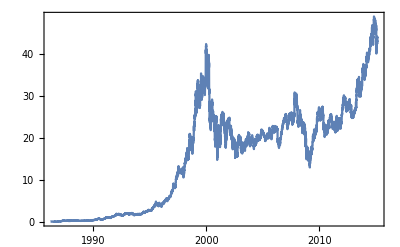

```mathematica
DateListPlot[msftDataset2[All,{"Date","Adj_Close"}]]
```

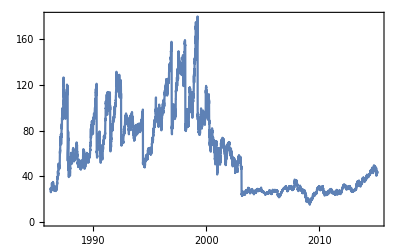

```mathematica
DateListPlot[msftDataset2[All,{"Date","Close"}]]
```

```mathematica
AddHistoricDatasetToDatabase[ticker_String,dataset_Dataset]:=
With[{conn=OpenSQLConnection[JDBC["PostgreSQL","localhost/ProjetC"]],
keys=Normal@Keys@First@dataset,
tableName="HISTORIC"},
SQLInsert[conn,tableName,{"Ticker"}~Join~keys,ArrayFlatten[{{"MSFT",Values@Normal@dataset[All,{"Date"->SQLDateTime}]}}]];
CloseSQLConnection[conn];
];
```